```mathematica
Needs["ErrorBarPlots`"]
Geräteliste
```

Geräteliste

Micrometerschraube	U=0.01mm

pro stab 5 gewichte
alu	5-75g
mes	50-250g
sta	100-1500g

## 1.

### Abmessungen Stab

1. alu 2. mes 3. sta in mm mit III/302/1

```mathematica
dataStab = {{"h", "b", "l", "d"}, {10.43, 2.08, 0, 0}, {10.00, 3.01, 0, 0}, {0, 0, 0, 5.98}}
dataStab=dataStab 10^-3
```

{{h,b,l,d},{10.43,2.08,0,0},{10.,3.01,0,0},{0,0,0,5.98}}

{{h/1000,b/1000,l/1000,d/1000},{0.01043,0.00208,0,0},{0.01,0.00301,0,0},{0,0,0,0.00598}}

```mathematica
dataStabFehler=0.01 10^-3
```

0.00001

### Messungen Gewichte

24, 14, 12 U = 2 g
andere U=0.001g

```mathematica
dataGewicht = {{"24", "14", "12", "8", "10", "22", "2", "4", "6", "18", "20"}, {195, 420, 222, 55.412, 111.666, 92.646, 5.542, 11.086, 10.941, 10.013, 10.146}}
```

{{24,14,12,8,10,22,2,4,6,18,20},{195,420,222,55.412,111.666,92.646,5.542,11.086,10.941,10.013,10.146}}

```mathematica
dataGewicht = dataGewicht*10^-3
```

{{24/1000,14/1000,12/1000,8/1000,10/1000,22/1000,2/1000,4/1000,6/1000,18/1000,20/1000},{39/200,21/50,111/500,0.055412,0.111666,0.092646,0.005542,0.011086,0.010941,0.010013,0.010146}}

```mathematica
dataGewichtFehler= 1 10^-3
```

1/1000

### Messungen Auflage

Messung mit Massband U = 1 mm

```mathematica
dataAuflage = {{"l"}, {500 10^-3}}
```

{{l},{1/2}}

```mathematica
dataAuflageFehler = 1 10^-3
```

1/1000

## 2.

### Alustab

```mathematica
dataAluGewicht = {5.542,10.941,10.941+10.013,55.412,55.412+5.542} 10^-3
```

{0.005542,0.010941,0.020954,0.055412,0.060954}

```mathematica
dataAlu0 = {{"2(5.5g)", "6(10.941)", "6+18(20g)", "8(55g)", "8+2 (60g)"}, {3.45, 3.5+0.04, 3.5+0.04, 7+0.47, 7.0+0.40}, {3.5+0.03, 3.0+0.48, 3.5+0.04, 7.5+0.09, 7.0+0.45}, {3.5+0.06, 3.5+0.08, 3.0+0.45, 7.5+0.06, 7.0+0.49}}
dataAluW = {{"2(5.5g)", "6(10.941)", "6+18(20g)", "8(55g)", "8+2 (60g)"}, {3.16, 2.5+0.46, 2.5+0.01, 4.5+0.06, 4.0+0.22}, {3+0.26, 2.5+0.42, 2.0+0.42, 4.5+0.09, 4.0+0.32}, {3+0.23, 3+0.08, 2.0+0.48, 4.5+0.10, 4.0+0.31}}
```

{{2(5.5g),6(10.941),6+18(20g),8(55g),8+2 (60g)},{3.45,3.54,3.54,7.47,7.4},{3.53,3.48,3.54,7.59,7.45},{3.56,3.58,3.45,7.56,7.49}}

{{2(5.5g),6(10.941),6+18(20g),8(55g),8+2 (60g)},{3.16,2.96,2.51,4.56,4.22},{3.26,2.92,2.42,4.59,4.32},{3.23,3.08,2.48,4.6,4.31}}

```mathematica
dataAlu = (dataAlu0-dataAluW) * 10^-3
```

{{0,0,0,0,0},{0.00029,0.00058,0.00103,0.00291,0.00318},{0.00027,0.00056,0.00112,0.003,0.00313},{0.00033,0.0005,0.00097,0.00296,0.00318}}

```mathematica
dataAluFehler = (0.01+0.01 )*10^-3
```

0.00002

```mathematica
AluM=Mean[dataAlu[[2;;4,All]]]
AluS= StandardDeviation[dataAlu[[2;;4,All]]]
AluF = AluS/(√3)
```

{0.000296667,0.000546667,0.00104,0.00295667,0.00316333}

{0.0000305505,0.0000416333,0.0000754983,0.0000450925,0.0000288675}

{0.0000176383,0.000024037,0.000043589,0.0000260342,0.0000166667}

### Messingtab

```mathematica
dataMesGewicht={10.013,111.666,55.412+111.666,195,195+55.412} 10^-3
```

{0.010013,0.111666,0.167078,39/200,0.250412}

```mathematica
dataMes0 = {{"8 50g", "10 100g", "8+10 150g", "24 200g", "24+8 250"}, {11.5+0.29, 11.5+0.33, 11.5+0.33, 11.5+0.34, 11.5+0.26}, {11.5+0.4, 11.5+0.35, 11.5+0.31, 11.5+0.33, 11.5+0.27}, {11.5+0.36, 11.5+0.46, 11.5+0.35, 11.5+0.31, 11.5+0.32}}
dataMesW = {{"8 50g", "10 100g", "8+10 150g", "24 200g", "24+8 250"}, {11+0.24, 10.0+0.44, 9.5+0.31, 9.5+0.09, 8.5+0.41}, {11+0.26, 10.0+0.46, 9.5+0.44, 9.5+0.17, 8.5+0.42}, {11.0+0.18, 10.5+0.06, 9.5+0.23, 9.5+0.03, 8.5+0.39}}
```

{{8 50g,10 100g,8+10 150g,24 200g,24+8 250},{11.79,11.83,11.83,11.84,11.76},{11.9,11.85,11.81,11.83,11.77},{11.86,11.96,11.85,11.81,11.82}}

{{8 50g,10 100g,8+10 150g,24 200g,24+8 250},{11.24,10.44,9.81,9.59,8.91},{11.26,10.46,9.94,9.67,8.92},{11.18,10.56,9.73,9.53,8.89}}

```mathematica
dataMes = (dataMes0-dataMesW)*10^-3
```

{{0,0,0,0,0},{0.00055,0.00139,0.00202,0.00225,0.00285},{0.00064,0.00139,0.00187,0.00216,0.00285},{0.00068,0.0014,0.00212,0.00228,0.00293}}

```mathematica
dataMesFehler = 10^-3(0.01+0.01)
```

0.00002

```mathematica
MesM=Mean[dataMes[[2;;4,All]]]
MesS= StandardDeviation[dataMes[[2;;4,All]]]
MesF = MesS/(√3)
```

{0.000623333,0.00139333,0.00200333,0.00223,0.00287667}

{0.0000665833,5.7735×10^-6,0.000125831,0.00006245,0.000046188}

{0.0000384419,3.33333×10^-6,0.0000726483,0.0000360555,0.0000266667}

### Stahlstab

```mathematica
Halterung in Gramm
```

Gramm Halterung in

```mathematica
HalteungGewicht=22.765
HalterungFehler = 0.001(*Nachschaun*)
```

22.765

0.001

```mathematica
dataSta0={{"10(111g)", "14(420g)", "12(222g)", "10+14", "12+14"}, {6.5+0.08, 6.5+0.28, 6.5+0.35, 6.5+0.21, 6.5+0.17}, {6.5+0.17, 6.5+0.14, 6.5+0.26, 6.5+0.18, 6.5+0.14}, {6.5+0.18, 6.5+0.21, 6.5+0.28, 6.5+0.22, 6.5+0.22}}
dataStaW={{"10(111g)", "14(420g)", "12(222g)", "10+14", "12+14"}, {6+0.43, 5.5+0.25, 6+0.27, 5.5+0.03, 5.0+0.28}, {6+0.40, 5.5+0.3, 6+0.28, 5.5+0.10, 5.0+0.28}, {6+0.48, 5.5+0.25, 6+0.30, 5.5+0.10, 5.0+0.25}}
```

{{10(111g),14(420g),12(222g),10+14,12+14},{6.58,6.78,6.85,6.71,6.67},{6.67,6.64,6.76,6.68,6.64},{6.68,6.71,6.78,6.72,6.72}}

{{10(111g),14(420g),12(222g),10+14,12+14},{6.43,5.75,6.27,5.53,5.28},{6.4,5.8,6.28,5.6,5.28},{6.48,5.75,6.3,5.6,5.25}}

```mathematica
dataSta = 10^-3(dataSta0-dataStaW)
```

{{0,0,0,0,0},{0.00015,0.00103,0.00058,0.00118,0.00139},{0.00027,0.00084,0.00048,0.00108,0.00136},{0.0002,0.00096,0.00048,0.00112,0.00147}}

```mathematica
dataStaFehler = (0.01+0.01)10^-3
```

0.00002

```mathematica
StaM=Mean[dataSta[[2;;4,All]]]
StaS= StandardDeviation[dataSta[[2;;4,All]]]
StaF = StaS/(√3)
```

{0.000206667,0.000943333,0.000513333,0.00112667,0.00140667}

{0.0000602771,0.0000960902,0.000057735,0.0000503322,0.0000568624}

{0.000034801,0.0000554777,0.0000333333,0.0000290593,0.0000328295}

```mathematica
dataStaGewicht={111.666,420,222,111.666+420,222+420} 10^-3
```

{0.111666,21/50,111/500,0.531666,321/500}

## 3.

```mathematica
dataAluPlot=Table[{dataAluGewicht[[i]],AluM[[i]]},{i,1,Length[AluM]}]
```

{{0.005542,0.000296667},{0.010941,0.000546667},{0.020954,0.00104},{0.055412,0.00295667},{0.060954,0.00316333}}

```mathematica
dataMesPlot=Table[{dataMesGewicht[[i]],MesM[[i]]},{i,1,Length[MesM]}]
```

{{0.010013,0.000623333},{0.111666,0.00139333},{0.167078,0.00200333},{39/200,0.00223},{0.250412,0.00287667}}

```mathematica
dataStaPlot=Table[{dataStaGewicht[[i]],StaM[[i]]},{i,1,Length[StaM]}]
```

{{0.111666,0.000206667},{21/50,0.000943333},{111/500,0.000513333},{0.531666,0.00112667},{321/500,0.00140667}}

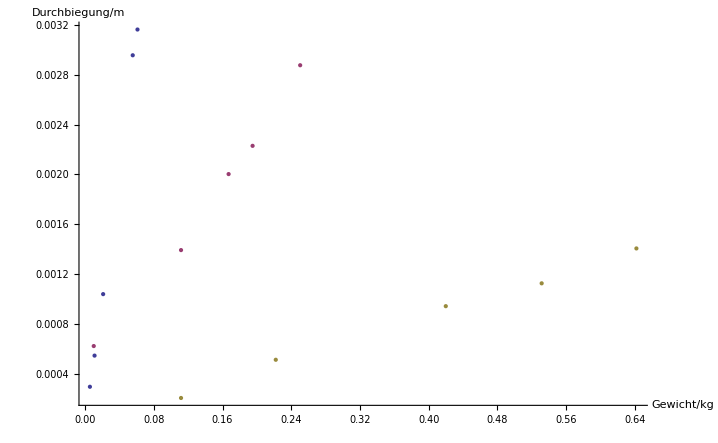

```mathematica
ListPlot[{dataAluPlot,dataMesPlot,dataStaPlot},AxesLabel->{"Gewicht/kg","Durchbiegung/m"}]
```

## 4.

### Linear Fit

```mathematica
AluFit=LinearModelFit[dataAluPlot,x,x]
```

FittedModel[-0.0000265618+0.0528998 x]

```mathematica
AluFitPara=AluFit["ParameterTableEntries"]
```

{{-0.0000265618,0.0000349854,-0.759224,0.502925},{0.0528998,0.00091092,58.0729,0.0000112483}}

```mathematica
MesFit=LinearModelFit[dataMesPlot,x,x]
```

FittedModel[0.000455904+0.00932639 x]

```mathematica
MesFitPara=MesFit["ParameterTableEntries"]
```

{{0.000455904,0.0000850634,5.35958,0.0127105},{0.00932639,0.000506158,18.4259,0.00034882}}

```mathematica
StaFit=LinearModelFit[dataStaPlot,x,x]
```

FittedModel[-7.70414×10^-6+0.00219744 x]

```mathematica
StaFitPara=StaFit["ParameterTableEntries"]
```

{{-7.70414×10^-6,0.0000362661,-0.212433,0.845384},{0.00219744,0.0000839554,26.1738,0.000122346}}

```mathematica
dataAluPlot=Table[{{dataAluGewicht[[i]],AluM[[i]]},ErrorBar[0.001,0.02]},{i,1,Length[AluM]}]
```

{{{0.005542,0.000296667},ErrorBar[0.001,0.02]},{{0.010941,0.000546667},ErrorBar[0.001,0.02]},{{0.020954,0.00104},ErrorBar[0.001,0.02]},{{0.055412,0.00295667},ErrorBar[0.001,0.02]},{{0.060954,0.00316333},ErrorBar[0.001,0.02]}}

{{{5.542,0.296667},ErrorBar[0.001,0.02]},{{10.941,0.546667},ErrorBar[0.001,0.03]},{{20.954,1.04},ErrorBar[0.002,0.05]},{{55.412,2.95667},ErrorBar[0.001,0.03]},{{60.954,3.16333},ErrorBar[0.002,0.02]}}

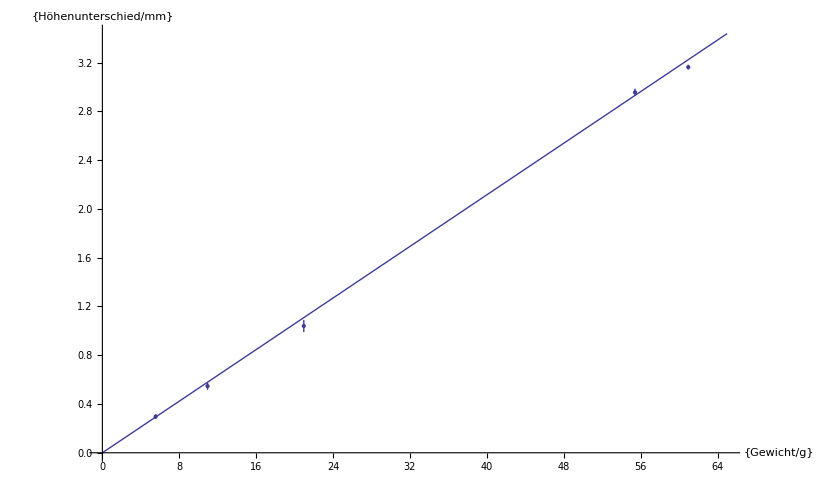

```mathematica
dataAluPlot={{{5.542,0.2966666666666667},ErrorBar[0.001,0.02]},{{10.941,0.5466666666666667},ErrorBar[0.001,0.03]},{{20.954,1.0400000000000003},ErrorBar[0.002,0.05]},{{55.412,2.956666666666667},ErrorBar[0.001,0.03]},{{60.954,3.163333333333334},ErrorBar[0.002,0.02]}}
Show[Plot[{AluFit[x]},{x,0,65}],ErrorListPlot[dataAluPlot],AxesLabel->{{"Gewicht/g"},{"Höhenunterschied/mm"}}]
```

```mathematica
dataMesPlot=Table[{{dataMesGewicht[[i]],MesM[[i]]},ErrorBar[0.001,0.02]},{i,1,Length[MesM]}]
```

{{{0.010013,0.000623333},ErrorBar[0.001,0.02]},{{0.111666,0.00139333},ErrorBar[0.001,0.02]},{{0.167078,0.00200333},ErrorBar[0.001,0.02]},{{39/200,0.00223},ErrorBar[0.001,0.02]},{{0.250412,0.00287667},ErrorBar[0.001,0.02]}}

{{{10.013,0.623333},ErrorBar[0.001,0.04]},{{111.666,1.39333},ErrorBar[0.001,0.01]},{{167.078,2.00333},ErrorBar[0.002,0.08]},{{195,2.23},ErrorBar[2.,0.04]},{{250.412,2.87667},ErrorBar[2.001,0.03]}}

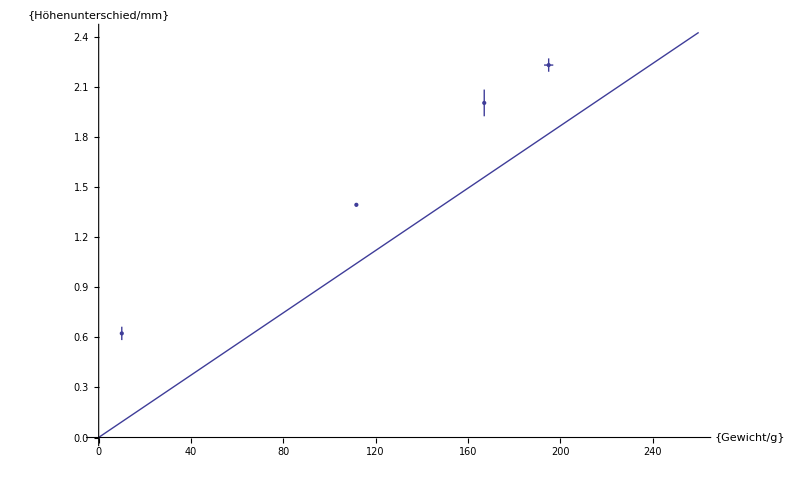

```mathematica
dataMesPlot={{{10.013,0.6233333333333331},ErrorBar[0.001,0.04]},{{111.666,1.3933333333333333},ErrorBar[0.001,0.01]},{{167.078,2.0033333333333334},ErrorBar[0.002,0.08]},{{195,2.2300000000000004},ErrorBar[2,0.04]},{{250.412,2.8766666666666665},ErrorBar[2.001,0.03]}}
Show[Plot[{MesFit[x]},{x,0,260}],ErrorListPlot[dataMesPlot],AxesLabel->{{"Gewicht/g"},{"Höhenunterschied/mm"}}]
```

```mathematica
dataStaPlot=Table[{{dataStaGewicht[[i]],StaM[[i]]},ErrorBar[0.001,0.02]},{i,1,Length[StaM]}]
```

{{{0.111666,0.000206667},ErrorBar[0.001,0.02]},{{21/50,0.000943333},ErrorBar[0.001,0.02]},{{111/500,0.000513333},ErrorBar[0.001,0.02]},{{0.531666,0.00112667},ErrorBar[0.001,0.02]},{{321/500,0.00140667},ErrorBar[0.001,0.02]}}

{{{111.666,0.206667},ErrorBar[0.001,0.04]},{{420,0.943333},ErrorBar[2.,0.06]},{{222,0.513333},ErrorBar[2.,0.04]},{{531.666,1.12667},ErrorBar[2.001,0.03]},{{642,1.40667},ErrorBar[4.,0.04]}}

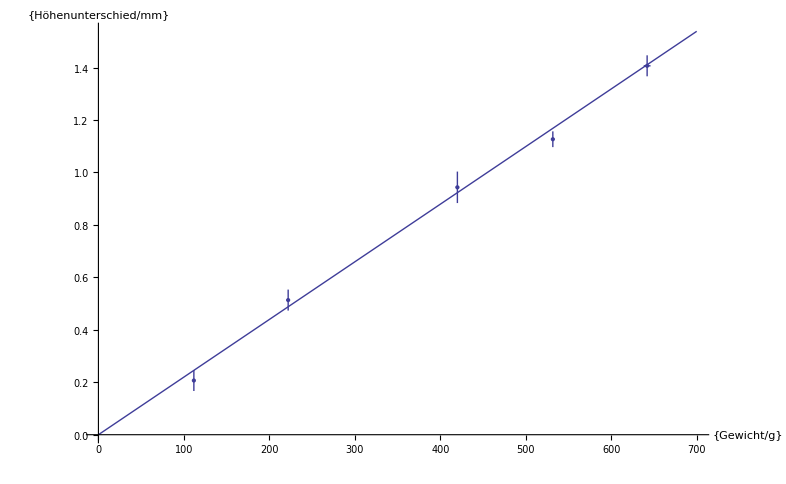

```mathematica
dataStaPlot={{{111.666,0.20666666666666642},ErrorBar[0.001,0.04]},{{420,0.9433333333333334},ErrorBar[2,0.06]},{{222,0.5133333333333333},ErrorBar[2,0.04]},{{531.6659999999999,1.1266666666666667},ErrorBar[2.001,0.03]},{{642,1.4066666666666663},ErrorBar[4,0.04]}}
Show[Plot[{StaFit[x]},{x,0,700}],ErrorListPlot[dataStaPlot],AxesLabel->{{"Gewicht/g"},{"Höhenunterschied/mm"}}]
```

### Flächenträgheitsmomente

#### Funktionen

```mathematica
fIAr[{h_,dh_,b_,db_}]:= {(b*h^3)/12,Abs[h^3/12]*db+Abs[(b* h^2)/4]*dh}(*rechteckiger Querschnitt*)
```

```mathematica
fIAk[{d_,dd_}]:={(Pi d^4)/64,Abs[(Pi d^3)/16]dd}(*kreis Querschnitt*)
```

#### Berechnung

```mathematica
dataIAr=Table[{dataStab[[i,2]],dataStabFehler,dataStab[[i,1]],dataStabFehler},{i,2,4}]
```

{{0.00208,0.00001,0.01043,0.00001},{0.00301,0.00001,0.01,0.00001},{0,0.00001,0,0.00001}}

```mathematica
IAr=Table [fIAr[dataIAr[[i,All]]],{i,1,3}]
```

{{7.82155×10^-12,1.2031×10^-13},{2.27258×10^-11,2.49228×10^-13},{0,0}}

```mathematica
dataIAk = Table[{dataStab[[i,4]],dataStabFehler},{i,2,4}]
```

{{0,0.00001},{0,0.00001},{0.00598,0.00001}}

```mathematica
IAk=Table [fIAk[dataIAk[[i,All]]],{i,1,3}]
```

{{0,0},{0,0},{6.27733×10^-11,4.19888×10^-13}}

### Elastizitätsmodul

```mathematica
g=9.81
```

9.81

```mathematica
fE[{k_,dk_,l_,dl_,IA_,dIA_}]:= {(l^3*g)/(48  k IA),Abs[(-l^3*g)/(48 IA k^2)]dk+Abs[(3 l^2 *g)/(48 IA k)]dl+Abs[(-l^3*g)/(48 k IA^2)]dIA}
```

#### AluStab

```mathematica
dataAluEr={AluFitPara[[2,1]],AluFitPara[[2,2]],dataAuflage[[2,1]],dataAuflageFehler,IAr[[1,1]],IAr[[1,2]]}
```

{0.0528998,0.00091092,1/2,1/1000,7.82155×10^-12,1.2031×10^-13}

```mathematica
fE[dataAluEr]
```

{6.17435×10^10,2.3834×10^9}

#### MessingStab

```mathematica
dataMesEr={MesFitPara[[2,1]],MesFitPara[[2,2]],dataAuflage[[2,1]],dataAuflageFehler,IAr[[2,1]],IAr[[2,2]]}
```

{0.00932639,0.000506158,1/2,1/1000,2.27258×10^-11,2.49228×10^-13}

```mathematica
fE[dataMesEr]
```

{1.20533×10^11,8.58657×10^9}

#### Stahlstab

```mathematica
dataStaEk={StaFitPara[[2,1]],StaFitPara[[2,2]],dataAuflage[[2,1]],dataAuflageFehler,IAk[[3,1]],IAk[[3,2]]}
```

{0.00219744,0.0000839554,1/2,1/1000,6.27733×10^-11,4.19888×10^-13}

```mathematica
fE[dataStaEk]
```

{1.85203×10^11,9.42589×10^9}

## 5.

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c])
```

```mathematica
spannung[m_,l_,I_,dm_,dl_,dI_]:=Module[{a,b,c,da,db,dc,f,fe},
f=(a*9.81 b/2)/(4 c);
fe=GError[f,{a,b,c},{da,db,dc}];
({f,fe}/.{a->m,b->l,c->I,da->dm,db->dl,dc->dI})]
```

```mathematica
spannung[Max[dataAluGewicht],dataStab[[2,2]],IAr[[1,1]],0.002 10^-3,dataStabFehler,IAr[[1,2]]]
spannung[Max[dataMesGewicht],dataStab[[3,2]],IAr[[2,1]],2.001 10^-3,dataStabFehler,IAr[[2,2]]]
spannung[Max[dataStaGewicht],dataStab[[4,4]],IAk[[3,1]],4. 10^-3,dataStabFehler,IAk[[3,2]]]
```

{1.9877×10^7,401960.}

{4.06708×10^7,906139.}

{7.49964×10^7,1.09433×10^6}

```mathematica
spannung[Max[dataAluGewicht],dataStab[[2,2]],IAr[[1,1]]]
```

{1.9877×10^7,Null}

```mathematica
spannung[Max[dataMesGewicht],dataStab[[3,2]],IAr[[2,1]]]
```

{4.06708×10^7,Null}

```mathematica
Max[dataStaGewicht]
dataStab[[4,4]]
IAk[[3,1]]
```

321/500

0.00598

6.27733×10^-11

```mathematica
spannung[Max[dataStaGewicht],dataStab[[4,4]],IAk[[3,1]]]
```

{7.49964×10^7,Null}